```mathematica
B:= A Exp[-2 ⅈ k a](k - ⅈ kprime Cot[kprime a])/(k + ⅈ  kprime Cot[kprime a])
```

```mathematica
kprime:= Sqrt[2 m (eng - v0) / ℏ]
```

```mathematica
Solve[ Exp[-2 ⅈ k a](k - ⅈ  kprime Cot[kprime a])/(k + ⅈ  kprime Cot[kprime a])== -Exp[ⅈ 2 δ], δ]
```

{{δ→ConditionalExpression[-1/2 ⅈ (2 ⅈ π C[1]+Log[-(ⅇ^(-2 ⅈ k) k)/(k+ⅈ √2 √(eng-v0) Cot[√2 √(eng-v0)])+(ⅈ √2 ⅇ^(-2 ⅈ k) √(eng-v0) Cot[√2 √(eng-v0)])/(k+ⅈ √2 √(eng-v0) Cot[√2 √(eng-v0)])]),C[1]∈ℤ]}}

```mathematica
ℏ:= 1
```

```mathematica
a:=1
```

```mathematica
m:=1
```

```mathematica
δ[eng_]:=  -1/2 ⅈ (Log[-(ⅇ^(-2 ⅈ k) k)/(k+ⅈ √2 √(eng-v0) Cot[√2 √(eng-v0)])+(ⅈ √2 ⅇ^(-2 ⅈ k) √(eng-v0) Cot[√2 √(eng-v0)])/(k+ⅈ √2 √(eng-v0) Cot[√2 √(eng-v0)])])
```

```mathematica
v0:= 30
```

```mathematica
k:=Sqrt[m eng ]
```

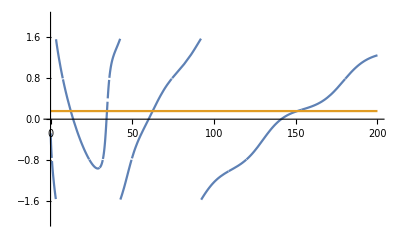

```mathematica
Plot[δ[eng],{eng,0.1, 200 }, PlotRange->{-2,2}]
```

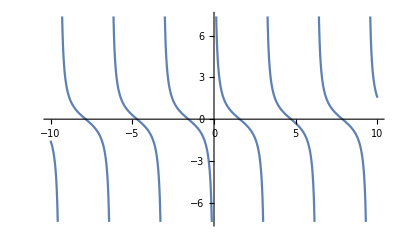

```mathematica
Plot[Cot[x],{x,-10,10}]
```